```mathematica
(* Figure out the rotation that puts the signal and idler into the pump coordinates. Here θ is the opening angle and ϕ is the azimuthal angle.
*)
RotX:= {{1, 0, 0},{0, Cos[θ],Sin[θ]}, {0, -Sin[θ], Cos[θ]}}
RotZ:={{ Cos[ϕ],Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0,0,1}}
RotY := {{ Cos[γ],0, -Sin[γ]}, {0,1,0},  {Sin[γ],0,  Cos[γ]}}

RotX:= {{1, 0, 0},{0, Cos[θ],-Sin[θ]}, {0, Sin[θ], Cos[θ]}}
RotZ:={{ Cos[ϕ],-Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}, {0,0,1}}
RotY := {{ Cos[γ],0, Sin[γ]}, {0,1,0},  {-Sin[γ],0,  Cos[γ]}}

RotZLab := RotY;
RotXLab := RotZ;
RotYLab := RotX;

RotTrans=RotX . RotZ
RotPumpwrtXtal = RotX.RotZ

Expand[RotXLab.{x1,y1,z1}//.{z1->Cos[Subscript[γ, p]]*x -Sin[Subscript[γ, p]]*z,x1-> y, y1-> Sin[Subscript[γ, p]]*x -Cos[Subscript[γ, p]]*z}]
```

{{Cos[ϕ],-Sin[ϕ],0},{Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ],-Sin[θ]},{Sin[θ] Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ]}}

{{Cos[ϕ],-Sin[ϕ],0},{Cos[θ] Sin[ϕ],Cos[θ] Cos[ϕ],-Sin[θ]},{Sin[θ] Sin[ϕ],Cos[ϕ] Sin[θ],Cos[θ]}}

{y Cos[ϕ]+z Cos[γ_p] Sin[ϕ]-x Sin[ϕ] Sin[γ_p],-z Cos[ϕ] Cos[γ_p]+y Sin[ϕ]+x Cos[ϕ] Sin[γ_p],x Cos[γ_p]-z Sin[γ_p]}

```mathematica
Subscript[x, s] := Cos[Subscript[ϕ, s]]*x -Sin[Subscript[ϕ, s]]*y 
Subscript[y, s]:= Cos[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*x + Cos[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y - Sin[Subscript[θ, s]]*z
Subscript[z, s]:=Sin[Subscript[θ, s]]*Sin[Subscript[ϕ, s]]*x + Sin[Subscript[θ, s]]*Cos[Subscript[ϕ, s]]*y + Cos[Subscript[θ, s]]*z

planarrules := {Subscript[ϕ, s] -> 0}
rulescoord :={Subscript[θ, s]->Subscript[θ, i],  Subscript[ϕ, s] -> π }

Subscript[x, i] = Subscript[x, s]//.rulescoord
Subscript[y, i]= Subscript[y, s]//.rulescoord
Subscript[z, i]= Subscript[z, s]//.rulescoord

Subscript[x, s] = Subscript[x, s] //. planarrules
Subscript[y, s]= Subscript[y, s]//.planarrules
Subscript[z, s]= Subscript[z, s]//.planarrules


(*Subscript[x, p] := x + Subscript[ρ, px]*z
Subscript[y, p]:= y*)

Subscript[x, p] = x;
Subscript[y, p]:= y

(* Introduce the assumption that the Rayleigh range is much longer than the crystal length and the waist can be treated as a constant. This dramatically simplifies things.
*)
rules2 :={Subscript[q, p] -> Subscript[W, p]^2 , Subscript[q, s] -> Subscript[W, s]^2 , Subscript[q, i] -> Subscript[W, i]^2 }
```

-x

-y Cos[θ_i]-z Sin[θ_i]

z Cos[θ_i]-y Sin[θ_i]

x

y Cos[θ_s]-z Sin[θ_s]

z Cos[θ_s]+y Sin[θ_s]

```mathematica
(* These are the normalization coefficients for the three Gaussians
*)
Subscript[n, s] = Subscript[W, s]/(Sqrt[π/2]*Subscript[q, s]) //.rules2;
Subscript[n, i] = Subscript[W, i]/(Sqrt[π/2]*Subscript[q, i]) //.rules2;
Subscript[n, p] = Subscript[W, p]/(Sqrt[π/2]*Subscript[q, p]) //. rules2;
```

```mathematica
(*Here is the argument in the exponential that we will want to integrate over wrt to x, y, and z.
*)
Arg1=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
```

-(x^2+(-y Cos[θ_i]-z Sin[θ_i])^2)/(2 q_i)-(x^2+y^2)/(2 q_p)-(x^2+(y Cos[θ_s]-z Sin[θ_s])^2)/(2 q_s)-ⅈ (x ΔK_x+y ΔK_y+z ΔK_z)

```mathematica
CompleteSquare[f_,x_]:=Module[{a,b,c},
{c,b,a}=CoefficientList[f,x];
a(x+b/2/a)^2+Simplify[(c-b^2/4/a)]
]
```

```mathematica
(* First we complete the square wrt to x. This makes it easier to analytically carry out the integration.
*)
Arg1 = CompleteSquare[Arg1, x]
```

(-1/(2 q_i)-1/(2 q_p)-1/(2 q_s)) (x-(ⅈ ΔK_x)/(2 (-1/(2 q_i)-1/(2 q_p)-1/(2 q_s))))^2+1/4 (-(2 (y Cos[θ_i]+z Sin[θ_i])^2)/q_i-(2 y^2)/q_p-(2 (y Cos[θ_s]-z Sin[θ_s])^2)/q_s-(2 q_i q_p q_s ΔK_x^2)/(q_p q_s+q_i (q_p+q_s))-4 ⅈ y ΔK_y-4 ⅈ z ΔK_z)

```mathematica
(* Now, the term in the b*(x-a)^2 term integrates to a constant*)
xconst:= Simplify[√π/-(-1/(2 Subscript[q, i])-1/(2 Subscript[q, p])-1/(2 Subscript[q, s])) //.rules2]
 
(*now we can do the remaining integral wrt y and complete the square agaim*)
yArg:= Simplify[1/4 (-(2 (y Cos[Subscript[θ, i]]+z Sin[Subscript[θ, i]])^2)/Subscript[q, i]-(2 y^2)/Subscript[q, p]-(2 (y Cos[Subscript[θ, s]]-z Sin[Subscript[θ, s]])^2)/Subscript[q, s]-(2 Subscript[q, i] Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Subscript[q, p]+Subscript[q, s]))-4 ⅈ y Subscript[ΔK, y]-4 ⅈ z Subscript[ΔK, z])]


(*Simplify[yArg]*)

yArg2=CompleteSquare[yArg,y]
```

(-Cos[θ_i]^2/(2 q_i)-1/(2 q_p)-Cos[θ_s]^2/(2 q_s)) (y+(-(z Cos[θ_i] Sin[θ_i])/q_i+(z Cos[θ_s] Sin[θ_s])/q_s-ⅈ ΔK_y)/(2 (-Cos[θ_i]^2/(2 q_i)-1/(2 q_p)-Cos[θ_s]^2/(2 q_s))))^2+1/4 (-(2 z^2 Sin[θ_i]^2)/q_i-(2 z^2 Sin[θ_s]^2)/q_s-(2 q_i q_p q_s ΔK_x^2)/(q_p q_s+q_i (q_p+q_s))+(q_p (z Sin[2 θ_i] q_s+q_i (-z Sin[2 θ_s]+2 ⅈ q_s ΔK_y))^2)/(2 q_i q_s (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-4 ⅈ z ΔK_z)

```mathematica
(*now the constant that remains after integrating over y is:*)
yconst = Simplify[ √π/-(-Cos[Subscript[θ, i]]^2/(2 Subscript[q, i])-1/(2 Subscript[q, p])-Cos[Subscript[θ, s]]^2/(2 Subscript[q, s]))//.rules2]
```

(2 √π)/(Cos[θ_i]^2/W_i^2+1/W_p^2+Cos[θ_s]^2/W_s^2)

```mathematica
(*This leaves the remaing z integrand*)
ArgZ:=1/4 (-(2 z^2 Sin[Subscript[θ, i]]^2)/Subscript[q, i]-(2 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]-(2 Subscript[q, i] Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Subscript[q, p]+Subscript[q, s]))+(Subscript[q, p] (z Sin[2 Subscript[θ, i]] Subscript[q, s]+Subscript[q, i] (-z Sin[2 Subscript[θ, s]]+2 ⅈ Subscript[q, s] Subscript[ΔK, y]))^2)/(2 Subscript[q, i] Subscript[q, s] (Cos[Subscript[θ, i]]^2 Subscript[q, p] Subscript[q, s]+Subscript[q, i] (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s])))-4 ⅈ z Subscript[ΔK, z])

ArgZ=Expand[ArgZ] 
(*Collect[ArgZ, z]*)
```

-(z^2 Sin[θ_i]^2)/(2 q_i)-(z^2 Sin[θ_s]^2)/(2 q_s)-(z^2 Sin[2 θ_i] Sin[2 θ_s] q_p)/(4 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(z^2 Sin[2 θ_s]^2 q_i q_p)/(8 q_s (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(z^2 Sin[2 θ_i]^2 q_p q_s)/(8 q_i (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-(q_i q_p q_s ΔK_x^2)/(2 (q_p q_s+q_i (q_p+q_s)))-(ⅈ z Sin[2 θ_s] q_i q_p ΔK_y)/(2 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(ⅈ z Sin[2 θ_i] q_p q_s ΔK_y)/(2 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-(q_i q_p q_s ΔK_y^2)/(2 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-ⅈ z ΔK_z

```mathematica
(*xconst := xconst //. rules2;
yconst := yconst //. rules2;*)
(* Now, we get rid of any terms that contain  Subscript[ρ, px]^2 or higher as they are negligible
*)
JJ = ArgZ/. { Subscript[ρ, px]^2 ->0}
ArgZ = Simplify[JJ];
(*ArgZ=Collect[ArgZ //.rules2,z]*)
```

-(z^2 Sin[θ_i]^2)/(2 q_i)-(z^2 Sin[θ_s]^2)/(2 q_s)-(z^2 Sin[2 θ_i] Sin[2 θ_s] q_p)/(4 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(z^2 Sin[2 θ_s]^2 q_i q_p)/(8 q_s (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(z^2 Sin[2 θ_i]^2 q_p q_s)/(8 q_i (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-(q_i q_p q_s ΔK_x^2)/(2 (q_p q_s+q_i (q_p+q_s)))-(ⅈ z Sin[2 θ_s] q_i q_p ΔK_y)/(2 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))+(ⅈ z Sin[2 θ_i] q_p q_s ΔK_y)/(2 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-(q_i q_p q_s ΔK_y^2)/(2 (Cos[θ_i]^2 q_p q_s+q_i (Cos[θ_s]^2 q_p+q_s)))-ⅈ z ΔK_z

```mathematica
Collect[ArgZ,z] //. rules2
```

1/8 z^2 (-(4 Sin[θ_s]^2 W_i^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))-(4 Sin[θ_i+θ_s]^2 W_p^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))-(4 Sin[θ_i]^2 W_s^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))+1/8 W_i^2 W_p^2 W_s^2 (-(4 ΔK_x^2)/(W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2))-(4 ΔK_y^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))+1/8 z (-(8 ⅈ W_i^2 W_s^2 ΔK_z)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))+(4 ⅈ W_p^2 W_s^2 (Sin[2 θ_i] ΔK_y-2 Cos[θ_i]^2 ΔK_z))/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2))-(8 ⅈ Cos[θ_s] W_i^2 W_p^2 (Sin[θ_s] ΔK_y+Cos[θ_s] ΔK_z))/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

```mathematica
(* The integral has a familar form. Let's see if Mathematica can do the integration straight up. Otherwise, compare it to a known solution
*)
(*IntZ:=Simplify[Exp[ArgZ] *yconst*xconst//. rules2]
Assuming[Subscript[W, i]>0  &&  Subscript[W, s]>0  && Subscript[W, p]>0 && Subscript[ΔK, x]>0 && Subscript[ΔK, y]>0 && Subscript[ΔK, z]>0  && Subscript[θ, i]>0 && Subscript[θ, s]>0,   Integrate[IntZ, {z,0,L}]]*)
```

```mathematica
(* Mathematica can't integrate this. Look at coefficients for the integral to get it in the right form*)
AA= Simplify[-1/8(-(4 Sin[Subscript[θ, s]]^2 Subscript[W, i]^2)/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))-(4 Sin[Subscript[θ, i]+Subscript[θ, s]]^2 Subscript[W, p]^2)/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))-(4 Sin[Subscript[θ, i]]^2 Subscript[W, s]^2)/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))]
BB=Simplify[(-1/ⅈ 1/8 (-(8 ⅈ Subscript[W, i]^2 Subscript[W, s]^2 Subscript[ΔK, z])/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))+(4 ⅈ Subscript[W, p]^2 Subscript[W, s]^2 (Sin[2 Subscript[θ, i]] Subscript[ΔK, y]-2 Cos[Subscript[θ, i]]^2 Subscript[ΔK, z]))/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))-(8 ⅈ Cos[Subscript[θ, s]] Subscript[W, i]^2 Subscript[W, p]^2 (Sin[Subscript[θ, s]] Subscript[ΔK, y]+Cos[Subscript[θ, s]] Subscript[ΔK, z]))/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2))))]
CC=Simplify[ - 1/8 Subscript[W, i]^2 Subscript[W, p]^2 Subscript[W, s]^2 (-(4 Subscript[ΔK, x]^2)/(Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Subscript[W, p]^2+Subscript[W, s]^2))-(4 Subscript[ΔK, y]^2)/(Cos[Subscript[θ, i]]^2 Subscript[W, p]^2 Subscript[W, s]^2+Subscript[W, i]^2 (Cos[Subscript[θ, s]]^2 Subscript[W, p]^2+Subscript[W, s]^2)))]

IZ:=- AA*z^2 -ⅈ*BB*z - CC
```

(Sin[θ_s]^2 W_i^2+Sin[θ_i+θ_s]^2 W_p^2+Sin[θ_i]^2 W_s^2)/(2 (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

(W_p^2 W_s^2 (-Sin[2 θ_i] ΔK_y+2 Cos[θ_i]^2 ΔK_z)+2 W_i^2 (W_s^2 ΔK_z+Cos[θ_s] W_p^2 (Sin[θ_s] ΔK_y+Cos[θ_s] ΔK_z)))/(2 (Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

-1/8 W_i^2 W_p^2 W_s^2 (-(4 ΔK_x^2)/(W_p^2 W_s^2+W_i^2 (W_p^2+W_s^2))-(4 ΔK_y^2)/(Cos[θ_i]^2 W_p^2 W_s^2+W_i^2 (Cos[θ_s]^2 W_p^2+W_s^2)))

```mathematica
(* While AA, BB, and CC look initially ugly, they simplify down somewhat. This leaves us with real coefficients for z^2 and imaginary coefficents for z. Now, this integral leads to error functions. Instead, look at Taylor expanding what is in the integrand and then carry out the integral.*)

IntResult=Normal[Assuming[R>-inf && S>-inf && T>-inf , Integrate[Series[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,15}],{z,0,L}]]]
```

ⅇ^-T L-1/2 ⅈ ⅇ^-T L^2 S-1/6 ⅇ^-T L^3 (2 R+S^2)+1/24 ⅈ ⅇ^-T L^4 S (6 R+S^2)+1/120 ⅇ^-T L^5 (12 R^2+12 R S^2+S^4)-1/720 ⅈ ⅇ^-T L^6 S (60 R^2+20 R S^2+S^4)-(ⅇ^-T L^7 (120 R^3+180 R^2 S^2+30 R S^4+S^6))/5040+(ⅈ ⅇ^-T L^8 S (840 R^3+420 R^2 S^2+42 R S^4+S^6))/40320+(ⅇ^-T L^9 (1680 R^4+3360 R^3 S^2+840 R^2 S^4+56 R S^6+S^8))/362880-(ⅈ ⅇ^-T L^10 S (15120 R^4+10080 R^3 S^2+1512 R^2 S^4+72 R S^6+S^8))/3628800-(ⅇ^-T L^11 (30240 R^5+75600 R^4 S^2+25200 R^3 S^4+2520 R^2 S^6+90 R S^8+S^10))/39916800+(ⅈ ⅇ^-T L^12 S (332640 R^5+277200 R^4 S^2+55440 R^3 S^4+3960 R^2 S^6+110 R S^8+S^10))/479001600+(ⅇ^-T L^13 (665280 R^6+1995840 R^5 S^2+831600 R^4 S^4+110880 R^3 S^6+5940 R^2 S^8+132 R S^10+S^12))/6227020800-(ⅈ ⅇ^-T L^14 S (8648640 R^6+8648640 R^5 S^2+2162160 R^4 S^4+205920 R^3 S^6+8580 R^2 S^8+156 R S^10+S^12))/87178291200-(ⅇ^-T L^15 (17297280 R^7+60540480 R^6 S^2+30270240 R^5 S^4+5045040 R^4 S^6+360360 R^3 S^8+12012 R^2 S^10+182 R S^12+S^14))/1307674368000+(ⅈ ⅇ^-T L^16 S (259459200 R^7+302702400 R^6 S^2+90810720 R^5 S^4+10810800 R^4 S^6+600600 R^3 S^8+16380 R^2 S^10+210 R S^12+S^14))/20922789888000

```mathematica
(* So, by doing the series expansion to the 5th order, we can easily find the integral. Here R = AA, S = BB, and T= CC. This isn't terrible as AA, BB, and CC are just constants and can be individually evaluated easily.  At the bottom of this workbook I test how valid this approximation is. As long as L*Sqrt[R] <1 the error should be less than ~1%. As L*Sqrt[R] <<1, the approx is very good.
*)
(*Simplify[IntResult //.{R -> AA, S -> BB, T -> CC}]*)

(*If we assume that Ws = Wi, then we get even further simplification. Don't think I want to do this in the final program.*)
AAsame = Simplify[AA //. {Subscript[W, i] -> Subscript[W, s]}]
BBsame = Simplify[BB //. {Subscript[W, i] -> Subscript[W, s]}]
CCsame = Simplify[CC //. {Subscript[W, i] -> Subscript[W, s]}]
```

(Sin[θ_i+θ_s]^2 W_p^2+(Sin[θ_i]^2+Sin[θ_s]^2) W_s^2)/(2 W_s^2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))

(2 W_s^2 ΔK_z+W_p^2 ((-Sin[2 θ_i]+Sin[2 θ_s]) ΔK_y+(2+Cos[2 θ_i]+Cos[2 θ_s]) ΔK_z))/(2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2))

-1/8 W_p^2 W_s^4 (-(4 ΔK_x^2)/(2 W_p^2 W_s^2+W_s^4)-(4 ΔK_y^2)/(W_s^2 ((Cos[θ_i]^2+Cos[θ_s]^2) W_p^2+W_s^2)))

```mathematica
(*OK, now what if we substitute in the values for q_p and q_s. Need to start over!

Arg2:=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(x^2+y^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)

rules1 :={Subscript[q, p] -> Subscript[W, p]^2 + 2*ⅈ*z/Subscript[k, p], Subscript[q, s] -> Subscript[W, s]^2 - 2*ⅈ*Subscript[z, s]/Subscript[k, s], Subscript[q, i] -> Subscript[W, i]^2 - 2*ⅈ*Subscript[z, i]/Subscript[k, i], Subscript[z, s] -> -Sin[Subscript[θ, s]]*y + Cos[Subscript[θ, s]]*z, Subscript[z, i] -> -Sin[Subscript[θ, i]]*y + Cos[Subscript[θ, i]]*z} 


Arg2 =Simplify[ Arg2 //. rules1] *)

(*Turns out this is way to hard. Going to ignore it*)
```

```mathematica
(* OK, so now I need to find the collection rate into just one of the fibers. This is done by dropping the Gaussian integral of the idler photon, then repeating the same procedure.
*)

ArgSingles=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, p])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z);
ArgCoinc :=-1/(2*Subscript[q, s])*(Subscript[x, s]^2+Subscript[y, s]^2)-1/(2*Subscript[q, i])(Subscript[x, i]^2+Subscript[y, i]^2)-1/(2*Subscript[q, p])*(Subscript[x, p]^2+Subscript[y, p]^2) - ⅈ*(Subscript[ΔK, x]*x + Subscript[ΔK, y]*y+Subscript[ΔK, z]*z)
ArgCoinc /. {Subscript[q, i]-> ∞};

ArgS = CompleteSquare[ArgSingles, x]
```

(-1/(2 q_p)-1/(2 q_s)) (x-(ⅈ ΔK_x)/(2 (-1/(2 q_p)-1/(2 q_s))))^2+1/4 (-(2 y^2)/q_p-(2 (y Cos[θ_s]-z Sin[θ_s])^2)/q_s-(2 q_p q_s ΔK_x^2)/(q_p+q_s)-4 ⅈ y ΔK_y-4 ⅈ z ΔK_z)

```mathematica
xconsts := Simplify[(√π)/(√-(-1/(2 Subscript[q, p])-1/(2 Subscript[q, s])))//. rules2]
yints :=1/4 (-(2 y^2)/Subscript[q, p]-(2 (y Cos[Subscript[θ, s]]-z Sin[Subscript[θ, s]])^2)/Subscript[q, s]-(2 Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(Subscript[q, p]+Subscript[q, s])-4 ⅈ y Subscript[ΔK, y]-4 ⅈ z Subscript[ΔK, z])
yints = CompleteSquare[yints, y]
```

(-1/(2 q_p)-Cos[θ_s]^2/(2 q_s)) (y+((z Cos[θ_s] Sin[θ_s])/q_s-ⅈ ΔK_y)/(2 (-1/(2 q_p)-Cos[θ_s]^2/(2 q_s))))^2+1/4 (-(2 z^2 Sin[θ_s]^2)/q_s-(2 q_p q_s ΔK_x^2)/(q_p+q_s)-(2 q_p (ⅈ z Cos[θ_s] Sin[θ_s]+q_s ΔK_y)^2)/(q_s (Cos[θ_s]^2 q_p+q_s))-4 ⅈ z ΔK_z)

```mathematica
(* This leaves us with the y constant and the z integrand
*)

yconsts := Simplify[(√π)/(√-(-1/(2 Subscript[q, p])-Cos[Subscript[θ, s]]^2/(2 Subscript[q, s]))) //. rules2]
zints :=1/4 (-(2 z^2 Sin[Subscript[θ, s]]^2)/Subscript[q, s]-(2 Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(Subscript[q, p]+Subscript[q, s])-(2 Subscript[q, p] (ⅈ z Cos[Subscript[θ, s]] Sin[Subscript[θ, s]]+Subscript[q, s] Subscript[ΔK, y])^2)/(Subscript[q, s] (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]))-4 ⅈ z Subscript[ΔK, z])
(*Now make the subsitution where we assume that the waist is constant in the crystal
*)

zints= Expand[zints] /. {Subscript[ρ, px]^2 ->0}
zints = Collect[zints 2, z]
```

-(z^2 Sin[θ_s]^2)/(2 q_s)+(z^2 Cos[θ_s]^2 Sin[θ_s]^2 q_p)/(2 q_s (Cos[θ_s]^2 q_p+q_s))-(q_p q_s ΔK_x^2)/(2 (q_p+q_s))-(ⅈ z Cos[θ_s] Sin[θ_s] q_p ΔK_y)/(Cos[θ_s]^2 q_p+q_s)-(q_p q_s ΔK_y^2)/(2 (Cos[θ_s]^2 q_p+q_s))-ⅈ z ΔK_z

2 z^2 (-Sin[θ_s]^2/(2 q_s)+(Cos[θ_s]^2 Sin[θ_s]^2 q_p)/(2 q_s (Cos[θ_s]^2 q_p+q_s)))+2 (-(q_p q_s ΔK_x^2)/(2 (q_p+q_s))-(q_p q_s ΔK_y^2)/(2 (Cos[θ_s]^2 q_p+q_s)))+2 z (-(ⅈ Cos[θ_s] Sin[θ_s] q_p ΔK_y)/(Cos[θ_s]^2 q_p+q_s)-ⅈ ΔK_z)

```mathematica
(* Same form of the integral before. Now we have:
*)
Subscript[AA, singles]=Simplify[ -2 (-Sin[Subscript[θ, s]]^2/(2 Subscript[q, s])+(Cos[Subscript[θ, s]]^2 Sin[Subscript[θ, s]]^2 Subscript[q, p])/(2 Subscript[q, s] (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s])))//. rules2]

Subscript[BB, singles]= Simplify[-2 /ⅈ (-(ⅈ Cos[Subscript[θ, s]] Sin[Subscript[θ, s]] Subscript[q, p] Subscript[ΔK, y])/(Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s])-ⅈ Subscript[ΔK, z]) //.rules2]


Subscript[CC, singles]=Simplify[ -2 (-(Subscript[q, p] Subscript[q, s] Subscript[ΔK, x]^2)/(2 (Subscript[q, p]+Subscript[q, s]))-(Subscript[q, p] Subscript[q, s] Subscript[ΔK, y]^2)/(2 (Cos[Subscript[θ, s]]^2 Subscript[q, p]+Subscript[q, s]))) //. rules2]
```

Sin[θ_s]^2/(Cos[θ_s]^2 W_p^2+W_s^2)

2 ((Cos[θ_s] Sin[θ_s] W_p^2 ΔK_y)/(Cos[θ_s]^2 W_p^2+W_s^2)+ΔK_z)

W_p^2 W_s^2 (ΔK_x^2/(W_p^2+W_s^2)+ΔK_y^2/(Cos[θ_s]^2 W_p^2+W_s^2))

```mathematica
(* We can use the same series expansion for the integral, now with different coefficients.

First, let's look at the prefactors. The relationship for efficiency is E = Subscript[P, coinc] / Subscript[P, singles]
*)

(*prefactor= Simplify[(xconst*yconst)^2/(xconsts*yconsts)^2]*)
```

```mathematica
(* That worked out nicer than expected! Now let's try the ratio of the series expansion of the two integrals.
*)
inttest:= Exp[-T]*Exp[-z^2 *(R ) -z *(ⅈ*S)]

IntResultExact =Normal[Assuming[R>-inf && S>-inf && T>-inf , Integrate[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,L}]]];


Subscript[P, coinc] = Abs[Subscript[n, s]*Subscript[n, p]*Subscript[n, i] *xconst*yconst*IntResult]^2 /. {R -> AA, S -> BB, T -> CC};
(*Subscript[P, coinc] = (Subscript[n, s]*Subscript[n, i]*Subscript[n, p]*xconst * yconst)^2 *Subscript[P, coinc];*)

(*Subscript[P, singles]= Abs[IntResult]^2 //. {R -> Subscript[AA, singles], S -> Subscript[BB, singles], T -> Subscript[CC, singles]};*)
Subscript[P, singles]= Abs[ Subscript[n, s]*Subscript[n, p]*xconsts*yconsts*IntResult]^2 /. {R -> Subscript[AA, singles], S -> Subscript[BB, singles], T -> Subscript[CC, singles]};
(*Subscript[P, singles] = (Subscript[n, s]*Subscript[n, p]*xconsts * yconsts)^2 *Subscript[P, singles];*)
Subscript[P, singles]=Assuming[Subscript[W, p]>0 && Subscript[W, s]>0 && Subscript[W, i]>0, Subscript[P, singles] ] ;(*//. {Subscript[W, i]->1000000};*)

(*Subscript[P, singles] =  Abs[Subscript[n, s]*Subscript[n, p] *xconsts*yconsts*IntResult]^2 /. {R -> AA, S -> BB, T -> CC}; /. { Subscript[W, s]->∞};*)
Eff = Subscript[P, coinc]/Subscript[P, singles];

rules2a := { Subscript[θ, s] -> 0.01*π/180, Subscript[θ, i] -> 0.01*π/180 , Subscript[W, s] -> .0001, Subscript[W, i] -> .0001, Subscript[W, p]-> .001,   Subscript[ΔK, x] ->0,  Subscript[ΔK, y] -> 0, Subscript[ΔK, z]->0, L -> .001}
"expand"
rulesc := { Subscript[θ, s] -> 0.00*π/180, Subscript[θ, i] -> 0.00*π/180, Subscript[ΔK, x] ->0, Subscript[ΔK, z]->0 , Subscript[ΔK, y] -> 1}
testcoinc =Exp[-z^2 *(R ) -z *(ⅈ*S) - T] /.{R -> AA, S -> BB, T -> CC}   /. {Subscript[W, i]->0};
testsingles =Exp[-z^2 *(R ) -z *(ⅈ*S) - T] /.{R -> Subscript[AA, singles], S -> Subscript[BB, singles], T -> Subscript[CC, singles]}  ;
testcoinc - testsingles /.rulesc;
w:= 10
w^3/(3*w^2)/2;
w^2/(2*w);
"coeff"
Subscript[n, s]*Subscript[n, p]*Subscript[n, i] *xconst*yconst(**1.00001 /.rules2a*)
Subscript[n, s]*Subscript[n, p] *xconsts*yconsts /. {Subscript[θ, s] ->0}(**1.00001 /.rules2a*)
"coinc"
Subscript[P, coinc] /.rules2a
"singles"
Subscript[P, singles] /.rules2a 
"eff"
Subscript[P, coinc] / Subscript[P, singles] *1. /.rules2a

Abs[IntResultExact] /. {R -> Subscript[AA, singles], S -> Subscript[BB, singles], T -> Subscript[CC, singles]} /.  {Subscript[θ, i] -> 0.1*π/180 , Subscript[θ, s] ->  0.1*π/180, Subscript[ΔK, y] -> 0,Subscript[ΔK, x] ->0, Subscript[ΔK, z]->0};
"coinc";
Abs[IntResultExact] /. {R -> AA, S -> BB, T -> CC} /.  {Subscript[θ, i] -> 0.1*π/180 , Subscript[θ, s] ->  0.1*π/180, Subscript[ΔK, x] ->0, Subscript[ΔK, z]->0, Subscript[ΔK, y] -> 0};
"erf";
Erf[50]*1.0000000001;

Subscript[n, s]*Subscript[n, p] xconsts*yconsts;
(*Eff = Simplify[Eff]*)
(* This gets ugly in a hurry. abort!*)
```

expand

coeff

(8 √(2/π))/(W_i W_p (1/W_i^2+1/W_p^2+1/W_s^2) (Cos[θ_i]^2/W_i^2+1/W_p^2+Cos[θ_s]^2/W_s^2) W_s)

4/(W_p (1/W_p^2+1/W_s^2) W_s)

coinc

2.49617×10^-16

singles

1.56847×10^-7

eff

1.59147×10^-9

```mathematica
(* Let's test how accurate the order of the expansions is of the integral *)
(*
inttest:= N*Exp[-T]*Exp[-z^2 *(R ) -z *(ⅈ*S)]

IntResultExact = Assuming[R>-inf && S>-inf && T>-inf , Integrate[inttest,{z,0,L}]]
(*IntResult5E := Normal[Series[IntResultExact,{S,0,10}] //. { Erf[L √R] -> Series[ Erf[L √R], {L,0,10}]}]*)
(*IntResult15 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[Exp[-z^2 *(R ) -z *(ⅈ*S) - T],{z,0,15}]],{z,0,L}]]*)
IntResult5 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,5}]],{z,0,L}]]
IntResult3 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,3}]],{z,0,L}]]
IntResult1 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,1}]],{z,0,L}]]
IntResult7 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,7}]],{z,0,L}]]
IntResult9 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,9}]],{z,0,L}]]
IntResult15 := Assuming[R>-inf && S>-inf && T>-inf , Integrate[Normal[Series[inttest,{z,0,15}]],{z,0,L}]]*)
```

```mathematica
(* Consider a collinear, perfectly phasematched system with the signal and pump waists as 100 microns*)
rulessamle :={Subscript[W, i]  -> Subscript[W, s] ,  Subscript[θ, i]-> Subscript[θ, s], Subscript[θ, s] ->0*π/180, Subscript[W, s]  -> .01,  Subscript[W, p]  -> .01,  Subscript[ΔK, x] ->0,  Subscript[ΔK, y] ->0,  Subscript[ΔK, z] ->0,  Subscript[ρ, px] -> 0*π/180, Subscript[ϕ, s]->0}

AAtest := Subscript[AA, singles] //.rulessamle
BBtest := Subscript[BB, singles] //.rulessamle
CCtest := Subscript[CC, singles] //.rulessamle
 
(* Crystal length in meters*)
Lxtal := l

(* isvalidapprox should be < 1 to keep the errors in check with a 5th order series expansion*)
isvalidapprox = Lxtal *Sqrt[Abs[AAtest]];

"normalizations";
NN = Subscript[n, s]*Subscript[n, p]*xconsts*yconsts //.rulessamle;
NY= Subscript[n, s]*Subscript[n, i]*Subscript[n, p]*xconst*yconst //.rulessamle;
"coincidence"
Abs[Subscript[P, coinc]]^2 //.rulessamle //.{ L -> Lxtal}

rulessub := {R ->AAtest, S -> BBtest, T -> CCtest, L -> Lxtal, N -> 1}
"efficiency"
Eff//.rulessamle //.{ L -> Lxtal}

InE= IntResultExact //. rulessub;
InE / Lxtal;

Eff1 = Eff//. rulessamle;
Eff1 //. { L -> Lxtal}

Simplify[Subscript[n, s]*Subscript[n, i]*Subscript[n, p]*xconst * yconst /(Subscript[n, s]*Subscript[n, p]*xconsts * yconsts) //.{Subscript[θ, s]->0, Subscript[θ, i]->0}] //.rulessamle


(*diff7= (IntResult7-IntResult15) /IntResult15/L //. {R ->AAtest, S -> BBtest, T -> CCtest, L -> 0.001}
diff9= (IntResult9-IntResult15) /IntResult15/L //. {R ->AAtest, S -> BBtest, T -> CCtest, L -> 0.001}*)
```

coincidence

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

Power::infy: Infinite expression 1/√0. encountered.

Indeterminate

efficiency

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Indeterminate

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

Power::infy: Infinite expression 1/√0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Indeterminate

0.00354615

{7.72002×10^-7,0.00258324,0.0517189,0.34134,1.35878}

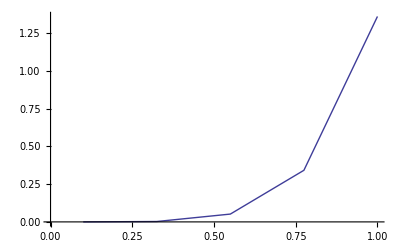

```mathematica
(* Now let's try to plot the error for 5th order expansion as a function of L*R. When there is perfect phasematching, then S and T go to 0. I am also setting L=1 to get a feel for how things scale. It should really be L*sqrt(R) that I investigate. *)
rulesplot :={ S -> 0, T -> 0,L->1,  N -> 1}
IE:=IntResultExact //.rulesplot
diff5plot := (IntResult9-IE)/IE //.rulesplot


(*data = Table[Abs[diff3plot*100], {R,.1, 1, .3}, {L,1, 2,.5}]
ListDensityPlot[data](*,  DataRange->{.1,1}]*)*)

data = Table[Abs[diff5plot*100], {R,.1, 2, .4}]
ListLinePlot[data, DataRange->{.1,1}]
(*Plot[Abs[diff3plot*100], {R, .1, 2}]*)
```

```mathematica
(* So it looks like the 5th order expansion is fine as long as L*R^0.5 << 1. Is there a better way to expand this without needing to go to a ton of terms? I tried it with the third order expansion and 9th order expansion. 
*)
```